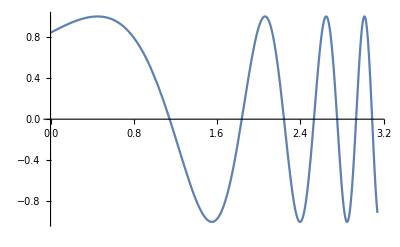

```mathematica
Plot[Sin[Exp[x]],{x,0,Pi}]
```

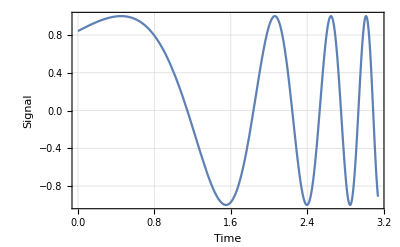

```mathematica
Show[ %, Frame -> True, FrameLabel -> {"Time", "Signal"}, GridLines -> Automatic ]
```

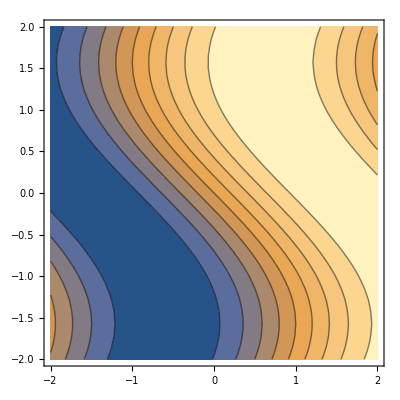

```mathematica
ContourPlot[Sin [x + Sin[y]], {x, -2, 2}, {y, -2, 2}]
```

```mathematica
Plot3D[ Sin[x + Sin[y]], {x, -3, 3}, {y, -3, 3}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[ {u Sin[t], u Cos[t], t/3}, {t, 0, 15}, {u, -1, 1}, Ticks -> None]
```

-Graphics3D-

```mathematica
ParametricPlot3D[ {Sin[t], Sin[2t] Sin [u], Sin[2t] Cos[u]}, {t, -Pi/2, Pi/2}, {u, 0, 2 Pi}, Ticks -> None ]
```

-Graphics3D-

```mathematica
Show[ %, %%]
```

ParametricPlot3D::pllim: Range specification {u,0,2,π} is not of the form {x, xmin, xmax}.

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics3D-,ParametricPlot3D[{Sin[t],Sin[2 t] Sin[u],Sin[2 t] Cos[u]},{t,-π/2,π/2},{u,0,2,π},Ticks→None]]

```mathematica
Show[ {Graphics3D[ {Cuboid[{0,0,0}], Cuboid[{2,2,2}], Cuboid[{2,1,3}], Cuboid[{3,2,1}], Cuboid[{2,1,1}]} ]}]
```

-Graphics3D-

```mathematica
Play[ Sin[10000 / t], {t, -4, 4} ]
```

```mathematica
Sound[SampledSoundFunction]CompiledFunction[…],64000,8000]]
```

Syntax::bktmop: Expression "Sound[SampledSoundFunction]CompiledFunction[DynamicModuleBox[{Typeset`open$$=False},PanelBox[«15»[«1»],«1»],DynamicModuleValues:>{}]],«5»,8000]" has no opening "[".